```mathematica
a1 = 6.22;
a2 = 6.121;
a3 = 0.005925;
a4 = 0.16326;
a5 = 6.48;
a6  = 11.4971;
a7 = 19.105;
a8 = 0.8938;
a9 = 6.54;
a10  = 11.4950;
a11 = -22.775;
a12 = 1.5707;
a13 = 4.3;
a14 = 14.08;
a15 = 27.80;
a16 = -1.653;
a17 = 1.50;
a18 = 14.67;
```

```mathematica
f0[x_]:= 1/(ⅇ^x+1);
```

```mathematica
zeta[xi_]:= (a1+a2*xi+a3*xi^3)/(1+a4*xi)*f0[a5(xi-a6)]+(a7+a8*xi)*f0[a9(a10-xi)]+(a11+a12*xi)*f0[a13(a14-xi)]+(a15+a16*xi)*f0[a17(a18-xi)];
```

```mathematica
Szeta5 = Normal[Series[zeta[xi],{xi,8,5}]]
```

0.0000509911 (xi-8)^5-0.000258713 (xi-8)^4+0.00530748 (xi-8)^3-0.0340057 (xi-8)^2+1.36113 (xi-8)+25.2477

```mathematica
Szeta6 = Normal[Series[zeta[xi],{xi,8,6}]]
```

3.84239×10^-6 (xi-8)^6+0.0000509911 (xi-8)^5-0.000258713 (xi-8)^4+0.00530748 (xi-8)^3-0.0340057 (xi-8)^2+1.36113 (xi-8)+25.2477

```mathematica
Szeta4 = Normal[Series[zeta[xi],{xi,8,4}]]
```

-0.000258713 (xi-8)^4+0.00530748 (xi-8)^3-0.0340057 (xi-8)^2+1.36113 (xi-8)+25.2477

```mathematica
Szeta50 = Normal[Series[zeta[xi],{xi,7,5}]];
```

```mathematica
NIntegrate[Abs[Szeta4-zeta[xi]],{xi,0,16}]
```

5.27272

```mathematica
NIntegrate[Abs[Szeta5-zeta[xi]],{xi,0,16}]
```

2.45386

```mathematica
NIntegrate[Abs[Szeta6-zeta[xi]],{xi,0,16}]
```

4.68599

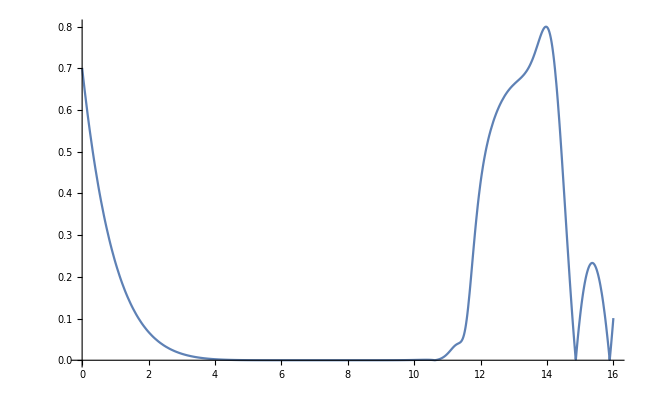

```mathematica
Plot[{Abs[Szeta5-zeta[xi]]},{xi,0,16},PlotRange-> Automatic,PlotLegends->"Expressions"]
```

```mathematica
InvSzeta5= Normal[InverseSeries[Series[zeta[xi],{xi,8,5}]]]
```

-1.92912×10^-6 (xi-25.2477)^5-0.0000638174 (xi-25.2477)^4-0.00105125 (xi-25.2477)^3+0.013485 (xi-25.2477)^2+0.734682 (xi-25.2477)+8

```mathematica
inv = InverseFunction[zeta]
```

zeta^(-1)

```mathematica
inv[27]
```

9.3225

```mathematica
expzeta[xi_]:=10^zeta[xi]
```

```mathematica
expzeta[10]
```

7.48497×10^27

```mathematica
inv[12]
```

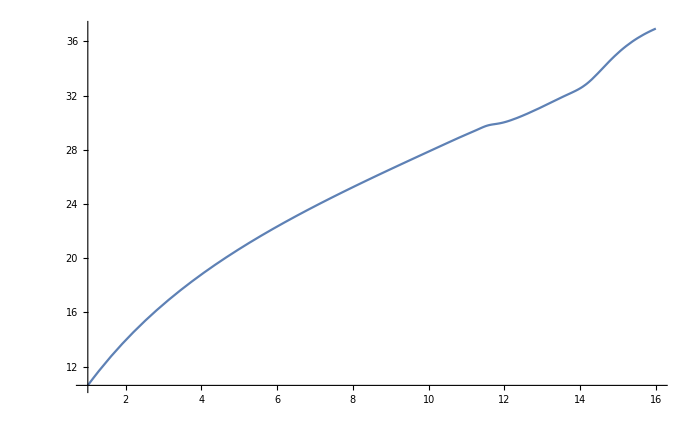

```mathematica
Plot[zeta[xi],{xi,1,16}]
```

```mathematica
inverse[z_] := -1.92912*10^-6 (z-25.2477)^5-0.0000638174 (z-25.2477)^4-0.00105125 (z-25.2477)^3+0.013485 (z-25.2477)^2+0.734682 (z-25.2477)+8
```

```mathematica
inverse[27]
```

9.3225

```mathematica
Error[z_] := Abs[inv[z]-inverse[z]]
```

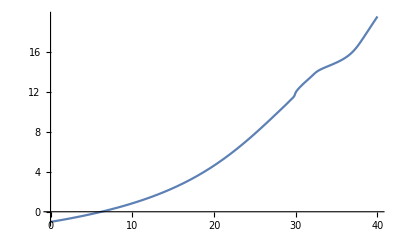

```mathematica
Plot[inv[z],{z,0,40}]
```

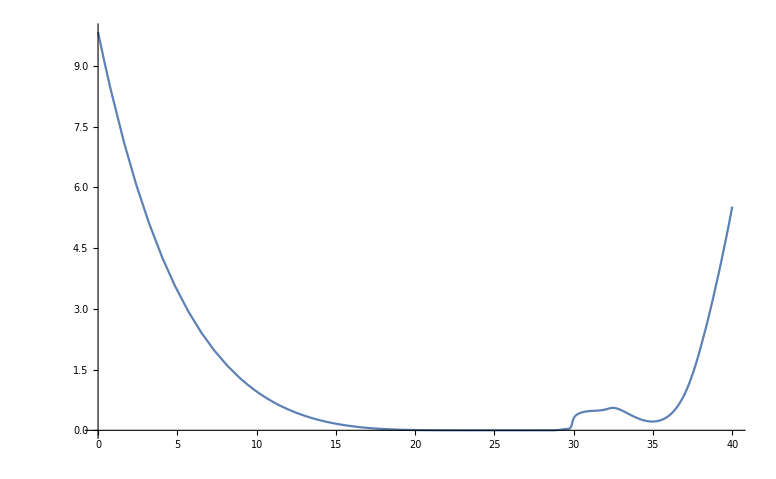

```mathematica
Plot[Error[z],{z,0,40}]
```

```mathematica
Sinv = Normal[Series[inv[z],{z,19.7,3}]]
```

0.000207887 (z-19.7)^3+0.0197301 (z-19.7)^2+0.530363 (z-19.7)+4.4597

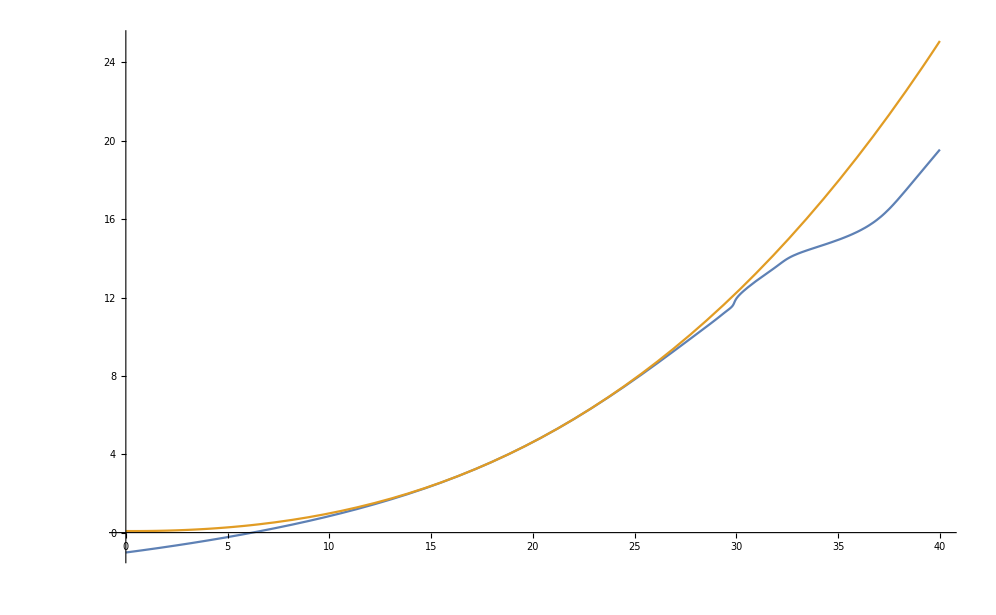

```mathematica
Plot[{inv[z],Sinv},{z,0,40}]
```

```mathematica
Sinv2= Normal[Series[inv[z],{z,37,4}]]
```

-0.0264787 (z-37)^4+0.0226411 (z-37)^3+0.214057 (z-37)^2+0.836664 (z-37)+16.0401

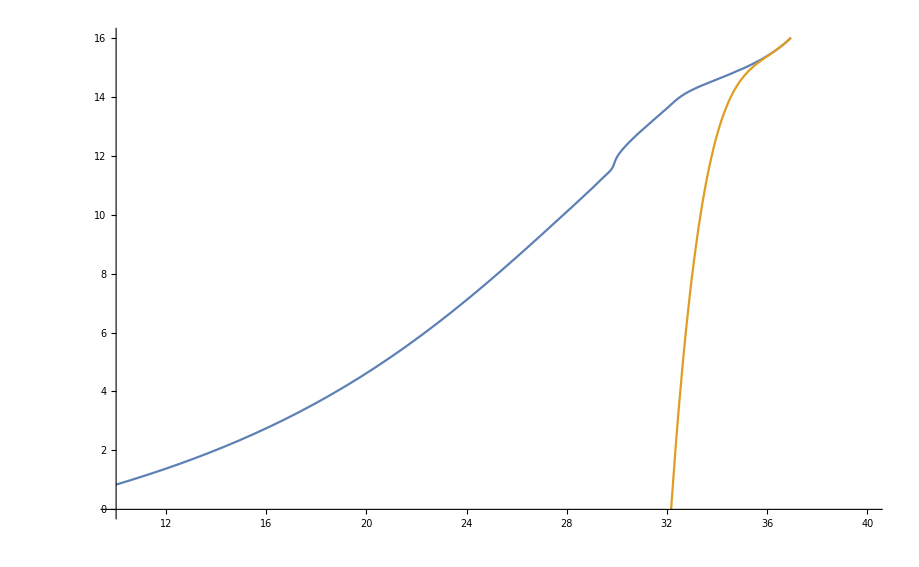

```mathematica
Plot[{inv[z],Sinv2},{z,10,40},PlotRange->{0,16}]
```